*Note: for the generational plots, left to right is better. 

This document is for looking at rules and being able to run variations of tag systems. We look at all binary numbers 0, 1, 00, 01, 10, 11, 000, 001, etc. and remove the first digit for the initial conditions. Generate the multi-way graph, the ListStepPlot across all initial conditions if available, and then create generational plots and branchial graphs. It is spectacular that you will find James, that yes bitmaps do make cloud notebooks visible and accessible!!!!!!

*********************Start with Post’s tag system.**************************
(0, left___, left___, s___) :> (s, 0, 0)
(1, left___, left___, s___) :> (s, 1, 1, 0, 1).

Before going into Post’s Tag System, some interesting thing to try from our friend Sinuhé Perea.

```mathematica
Dean = Labeled[ ResourceFunction["MultiwaySystem"][{"0" -> "00", "1" -> "1101"}, {"101"}, 3, "StatesGraph", ImageSize -> 1000], StringTemplate["{0}->`a` {1}->`b` `e`"] [<| "a" -> {0, 0}, "b" -> {1, 1, 0, 1}, "e" :> {1, 0, 1} |>]]
```

-Graphics-{0}->{0, 0} {1}->{1, 1, 0, 1} {1, 0, 1}

Start with Post’s Tag System.

```mathematica
generatePost[
rule1_,
rule2_,
init_,
timeSteps_
]:=Table[Labeled[NestGraph[ReplaceList[{
{0, left___,left___,s___}:>Flatten[{s,rule1}],
{1,left___,left___,s___}:>Flatten[{s,rule2}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["{0,0,s___}->`a`
{1,0,s___}->`b`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"e":>init
|>]
],
{t,1,timeSteps}]
```

```mathematica
generatePost[
{0,0},
{1,1,0,1},
{1,0,1},
5
]
```

-Graphics-

```mathematica
graphPost:= With[{
g=NestGraph[ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{{1,0,1}},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],
Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{0,left___,left___,s___}->`a`
{1,left___,left___,s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>{1,0,1}
|>]]]
```

```mathematica
graphPost
```

-Graphics-

```mathematica
rulePostAllInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{Tuples[{0,1},i][[j]]},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
```

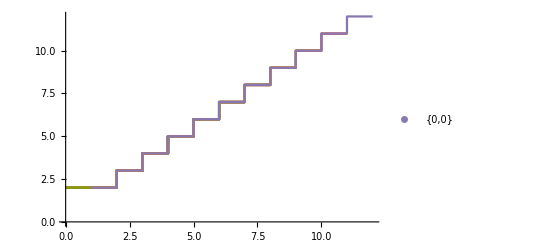
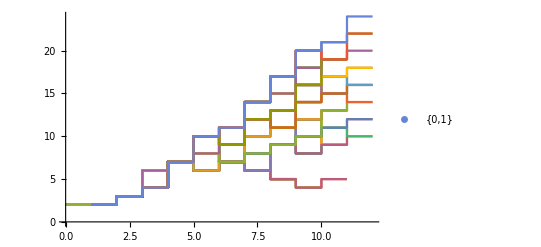
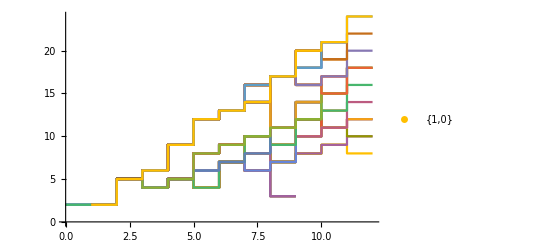
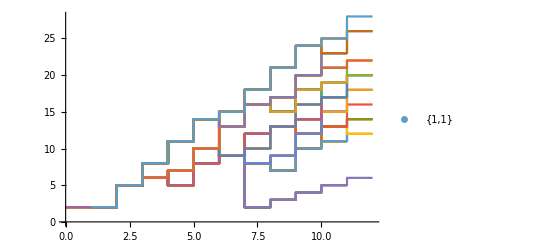
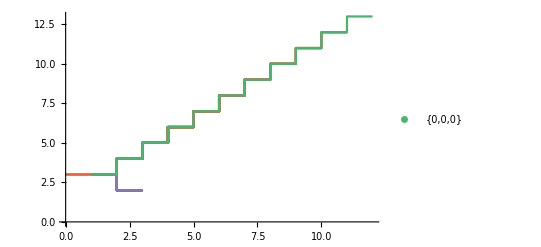
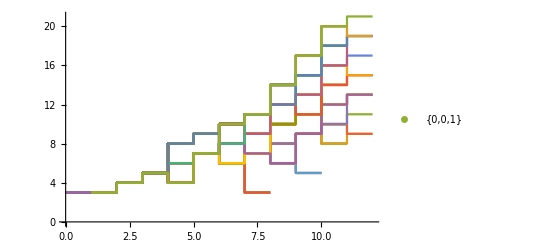
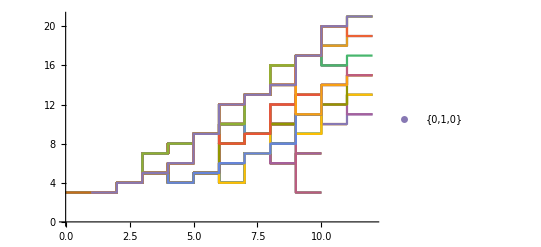
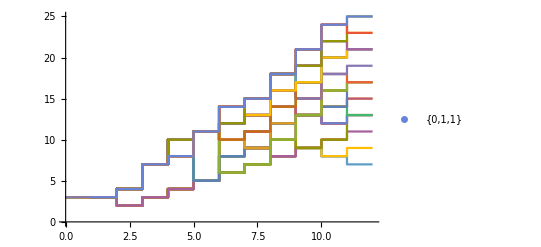

```mathematica
rulePostAllInitialConditions[{2,3},10]
```

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{{1,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

{11
11101,11
11101
011101,11
11101
11011101,11
11101
011101
10100,11
11101
011101
1110100,11
11101
11011101
10111011101,11
11101
011101
10100
01001101,11
11101
011101
1110100
1101001101,11
11101
11011101
10111011101
01110111011101,11
11101
011101
10100
01001101
100110100,11
11101
011101
1110100
1101001101
011011101,11
11101
011101
1110100
1101001101
1010011011101,11
11101
11011101
10111011101
01110111011101
1011101110100,11
11101
11011101
10111011101
01110111011101
111011101110100}

```mathematica
AllPathCanyons[g_]:=Table[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
{i,1,Length[VertexList[g]]}
]
```

```mathematica
AllPathCanyons[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{{1,0,1}},
8,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
]
```

-Graphics-

```mathematica
generateAllTemperaturePlots[
init_,
timeSteps_,
branchialGraph_:True,
matrixForm_:True
]:=With[{
graph=NestGraph[ReplaceList[
{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}
],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]
},
Table[
{
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{0,left___,left___,s___}->`a`
{1,left___,left___,s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>init
|>]],
If[branchialGraph,{{"[◼]", "BranchialGraph"}}[graph],Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]],FontSize->8],Null]
},
{t,1,timeSteps}
] 
]
```

```mathematica
generateAllTemperaturePlots[
{1,0,1},
5,
True,
True
]
```

NestGraph::intpm: Positive machine-sized integer expected at position 3 in NestGraph[ReplaceList[{{0,left___,left___,s___}:>{s,0,0},{1,left___,left___,s___}:>{s,1,1,0,1}}],{{1,0,1}},t].

ArrayPlot::mat: Argument $Aborted[] at position 1 is not a list of lists.

-Graphics-

**************Four-Rule Tag System*************. 
Now it is time to make a four-rule tag system with each rule performed individually.

```mathematica
generatePathCanyon[rule1_,
	rule2_,
	rule3_,
	rule4_,
	init_,
	timeSteps_]:=Table[Labeled[NestGraph[ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,rule1}],
{left___,1,0,s___}:>Flatten[{left,s,rule2}],
{left___,0,1,s___}:>Flatten[{left,s,rule3}],
{left___,1,1,s___}:>Flatten[{left,s,rule4}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["
{0,0}->`a`
{1,0}->`b`
{0,1}->`c`
{1,1}->`d`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"c":>rule3,
"d":>rule4,
"e":>init
|>]
],
{t,1,timeSteps}]
```

```mathematica
generatePathCanyon[
{0,0},
{1,1,0,1},
{1,0},
{1,1,1},
{1,0,1},
5
]
```

-Graphics-

```mathematica
graphFourWay:= With[{
g=NestGraph[ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0},
{left___,1,0,s___}:>{left,s,1,1,0,1},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,0,1}},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],
Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{left___,0,0,s___}->`a`
{left___,1,0,s___}->`b`
{left___,0,1,s___}->`c`
{left___,1,1,s___}->`d`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"c"->{1,0},
"d"->{1,1,1},
"e":>{1,0,1}
|>]]]
```

```mathematica
graphFourWay
```

-Graphics-

```mathematica
oneRuleAllInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{left___,0,0,s___}:>{left,s,0,0},
{left___,1,0,s___}:>{left,s,1,1,0,1},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}
}],
{{1,0,1}},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
```

```mathematica
oneRuleAllInitialConditions[{2,3},10]
```

-Graphics-

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,0,s___}:>Flatten[{left,s,1,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,1,0,1}]
}],
{{1,0,1}},
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

{101
1101,101
1110,101
1101
01101,101
1101
11101,101
1101
11110,101
1110
10101,101
1101
01101
001101,101
1101
01101
011101,101
1101
01101
011110,101
1101
01101
101110,101
1101
11101
101101,101
1101
11101
111101,101
1101
11101
111110,101
1101
11110
110101,101
1101
01101
001101
0001101,101
1101
01101
001101
0011101,101
1101
01101
001101
0011110,101
1101
01101
001101
0101110,101
1101
01101
001101
1101110,101
1101
01101
011101
0101101,101
1101
01101
011101
0111101,101
1101
01101
011101
0111110,101
1101
01101
011110
0110101,101
1101
01101
011110
1110110,101
1101
11101
101101
1001101,101
1101
01101
101110
1011101,101
1101
11101
101101
1011110,101
1101
11101
101101
1101101,101
1101
01101
101110
1010101,101
1101
01101
101110
1110101,101
1101
11101
111101
1111101,101
1101
11101
111101
1111110,101
1101
01101
001101
0001101
00001101,101
1101
01101
001101
0001101
00011101,101
1101
01101
001101
0001101
00011110,101
1101
01101
001101
0001101
00101110,101
1101
01101
001101
0001101
01101110,101
1101
01101
001101
0011101
00101101,101
1101
01101
001101
0011101
00111101,101
1101
01101
001101
0011101
00111110,101
1101
01101
001101
0011101
11101110,101
1101
01101
001101
0011110
00110101,101
1101
01101
001101
0011110
01110110,101
1101
01101
001101
0011110
11110110,101
1101
01101
011101
0101101
01001101,101
1101
01101
001101
0101110
01011101,101
1101
01101
011101
0101101
01011110,101
1101
01101
011101
0101101
01101101,101
1101
01101
001101
0101110
01010101,101
1101
01101
001101
0101110
01110101,101
1101
01101
011110
0110101
10101110,101
1101
01101
011101
0111101
01111101,101
1101
01101
011101
0111101
01111110,101
1101
11101
101101
1001101
10001101,101
1101
11101
101101
1001101
10011101,101
1101
11101
101101
1001101
10011110,101
1101
01101
101110
1011101
10101101,101
1101
01101
101110
1011101
10111101,101
1101
01101
101110
1011101
10111110,101
1101
01101
011110
1110110
11101101,101
1101
01101
011110
1110110
10110101,101
1101
01101
001101
1101110
11110101,101
1101
11101
101101
1101101
11001101,101
1101
01101
001101
1101110
11011101,101
1101
11101
101101
1101101
11011110,101
1101
01101
001101
1101110
11010101,101
1101
01101
011110
1110110
11100101,101
1101
11101
111101
1111101
11111101,101
1101
11101
111101
1111101
11111110}

```mathematica
AllPathCanyons[g_]:=Table[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
{i,1,Length[VertexList[g]]}
]
```

```mathematica
AllPathCanyons[
NestGraph[
ReplaceList[{
{left___,0,1,s___}:>{left,s,0,0},
{left___,1,1,s___}:>{left,s,1,1,0,1},
{left___,0,1,s___}:>{left,s,0,0,1},
{left___,1,1,s___}:>{left,s,0,0,1}
}],
{{1,0,1}},
8,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
]
```

-Graphics-

```mathematica
generateAllTemperaturePlots[
l1_,l2_,l3_,l4_,
i1R_,i2R_,i3R_,i4R_,
init_,
timeSteps_,
branchialGraph_:True,
matrixForm_:True
]:=With[{
graph=NestGraph[ReplaceList[
{
{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},l1][[i3]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},l2][[i4]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},l3][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},l4][[i4]]}]
}
],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]
},
Table[
{
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{left___,0,0,s___}->`a`
{left___,1,0,s___}->`b`
{left___,0,1,s___}->`c`
{left___,1,1,s___}->`d`
`e`"]
[<|
"a"->Tuples[{0,1},l1][[i1]],
"b"->Tuples[{0,1},l2][[i2]],
"c":>Tuples[{0,1},l3][[i3]],
"d":>Tuples[{0,1},l4][[i4]],
"e":>init
|>]],
If[branchialGraph,{{"[◼]", "BranchialGraph"}}[graph],Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]],FontSize->8],Null]
},
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]},
{i3,i3R[[1]],i3R[[2]]},
{i4,i4R[[1]],i4R[[2]]}
] 
]
```

```mathematica
generateAllTemperaturePlots[
3,3,3,3,
{8,8},{4,4},{8,8},{4,4},
{1,0,1},
5,
True,
True
]
```

-Graphics-

**************Two-Way Tag System*************

```mathematica
generatePathCanyon[rule1_,
	rule2_,
	init_,
	timeSteps_]:=Table[Labeled[NestGraph[ReplaceList[{
{left___,0,s___}:>Flatten[{left,s,rule1}],
{left___,1,s___}:>Flatten[{left,s,rule2}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"],
StringTemplate["
{0}->`a`
{1}->`b`
`e`"]
[<|
"a"->rule1,
"b"->rule2,
"e":>init
|>]
],
{t,1,timeSteps}]
```

```mathematica
generatePathCanyon[
{0,0},
{1,1,0,1},
{1,0,1},
5
]
```

{-Graphics-
{0}->{0, 0}
{1}->{1, 1, 0, 1}
{1, 0, 1},-Graphics-
{0}->{0, 0}
{1}->{1, 1, 0, 1}
{1, 0, 1},-Graphics-
{0}->{0, 0}
{1}->{1, 1, 0, 1}
{1, 0, 1},-Graphics-
{0}->{0, 0}
{1}->{1, 1, 0, 1}
{1, 0, 1},-Graphics-
{0}->{0, 0}
{1}->{1, 1, 0, 1}
{1, 0, 1}}

```mathematica
graphTwoWay:= With[{
g=NestGraph[ReplaceList[{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}],
{{0}},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Full]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],
Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{left___,0,s___}->`a`
{left___,1,s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>{0}
|>]]]
```

```mathematica
graphTwoWay
```

-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{0}

```mathematica
oneRuleAllInitialConditions[lengthInitialConditionR_,lastTimeStep_]:=
Table[ListStepPlot[Legended[FlattenAt[
 Table[
Style[Text[
With[
{
graph = NestGraph[
ReplaceList[{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}],
{{1}},
timeStep,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
},
Table[
Length /@FindShortestPath[graph,First[VertexList[graph]],VertexList[graph][[v]]],
{v,1,Length[VertexList[graph]]}
]
]]][[1]][[1]],
{timeStep,1,lastTimeStep}
]
,
{#}&/@Range[lastTimeStep]],Tuples[{0,1},i][[j]]]],
{i,lengthInitialConditionR[[1]],lengthInitialConditionR[[2]]},
{j,1,2^i}]
```

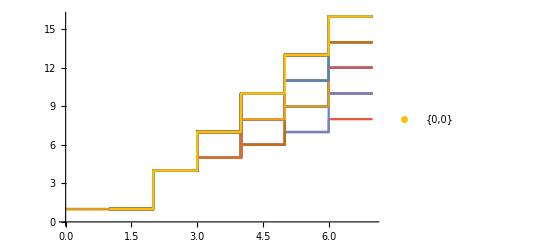
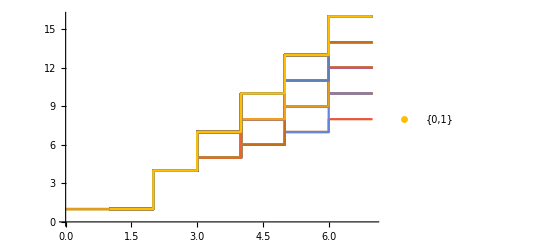
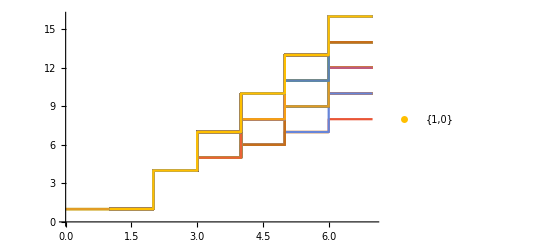
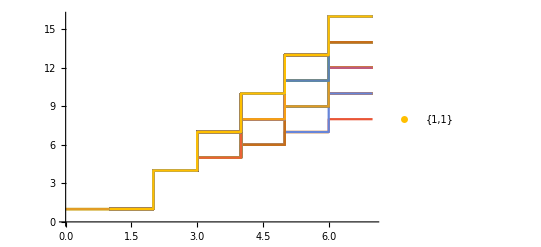
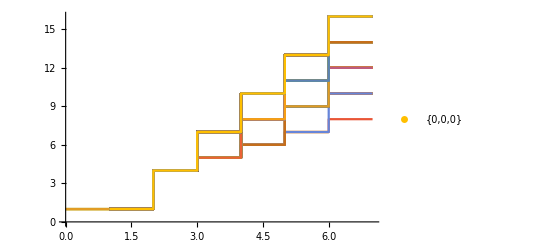
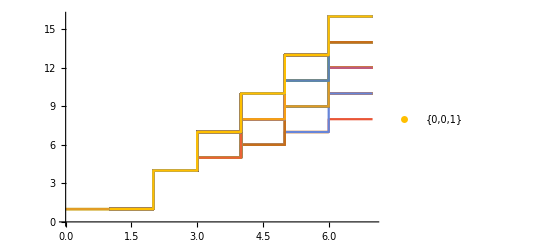
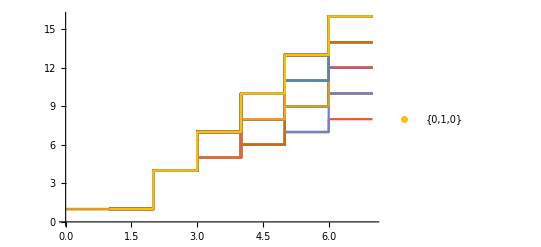
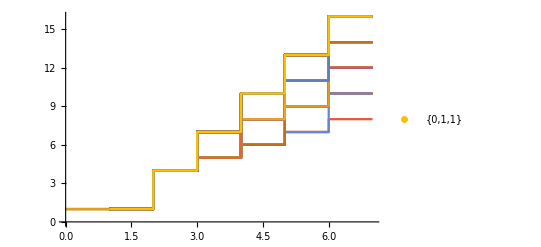

```mathematica
oneRuleAllInitialConditions[{2,3},5]
```

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[Table[
Column[Row/@PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[j]],
{Automatic,Automatic},
.25
],Center]//. 0.25->"",
{j,2,Length[VertexList[g]]}
]//.{x_}:>x],FontFamily->"Roboto"]
```

```mathematica
AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}],
{{1}},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

-Graphics-

```mathematica
OneDimensionAll[g_]:=Table[
ArrayPlot[
Reverse@Transpose[
PadRight[
With[
{
vertices=VertexList[g],
randomInit=Tuples[{0,1},3]
},
Table[
FindShortestPath[g,First[VertexList[g]],vertices[[i]]],
{i,1,Length[vertices]}
]
][[i]],
{Automatic,Automatic},
.25
]
],
Frame->True,
ColorRules->{0->Hue[.95,.4,1.4],
1->Hue[.1,.1,.1]},
Mesh->True
],
{i,1,Length[VertexList[g]]}
]
```

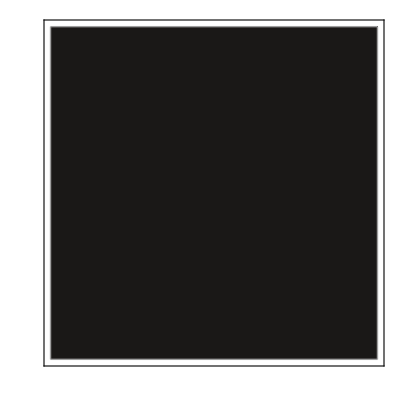
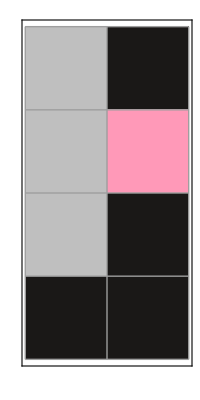
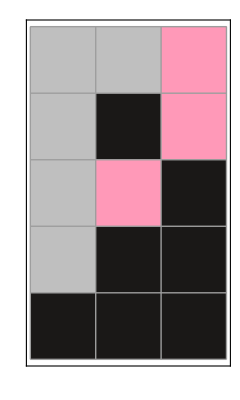
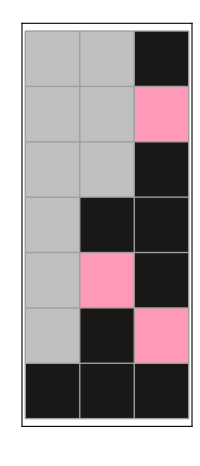
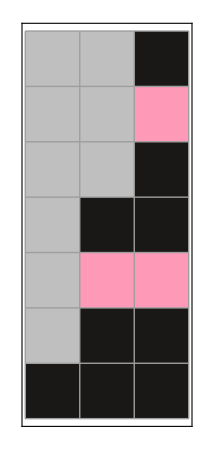
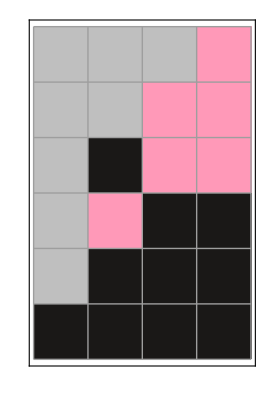
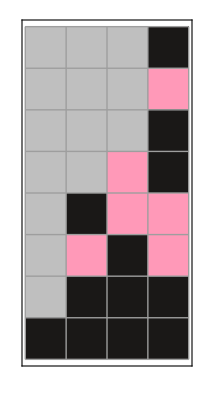
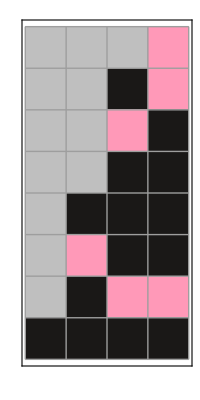

```mathematica
OneDimensionAll[
NestGraph[
ReplaceList[{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}],
{{1}},
4,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
]
```

```mathematica
OneDimensionAllAdjacency[
l1_,l2_,
i1R_,i2R_,
init_,
timeSteps_,
branchialGraph_:True,
matrixForm_:True
]:=With[{
graph=NestGraph[ReplaceList[
{
{left___,0,s___}:>{left,s,0,0},
{left___,1,s___}:>{left,s,1,1,0,1}
}
],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"]
},
Table[
{
Labeled[
ArrayPlot[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]/.∞->0,ColorFunction->"TemperatureMap", PlotLegends->Automatic],
StringTemplate["{left___,0,s___}->`a`
{left___,1,s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>init
|>]],
If[branchialGraph,{{"[◼]", "BranchialGraph"}}[graph],Null],
If[matrixForm,Style[MatrixForm[GraphDistanceMatrix[{{"[◼]", "BranchialGraph"}}[graph]]],FontSize->8],Null]
},
{t,1,timeSteps},
{i1, i1R[[1]],i1R[[2]]},
{i2,i2R[[1]],i2R[[2]]}
] 
]
```

```mathematica
OneDimensionAllAdjacency[
2,2,
{1,2^2},{1,2^2},
{1,1,0,1},
4,
True,
True
]
```

NestGraph::intpm: Positive machine-sized integer expected at position 3 in NestGraph[ReplaceList[{{left___,0,s___}:>{left,s,0,0},{left___,1,s___}:>{left,s,1,1,0,1}}],{{1,1,0,1}},t].

{{{{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}},{{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}},{{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}},{{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0)}}},2,{{{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(1)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(1)},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,1},{-Graphics-{left___,0,s___}->{0, 0}
{left___,1,s___}->{1, 1, 0, 1}
{1, 1, 0, 1},-Graphics-,(1)}},2,{1}}}
 |  |  |  |

Examples

```mathematica
graphPost:= With[{

g=ResourceFunction["NestGraphTagged"][ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}
}],
{{1,0,1}},
3,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality",
ImageSize->Large]},
Labeled[
HighlightGraph[
Graph[
g,
VertexLabels->Thread[VertexList[g]->(Length[#]&/@VertexList[g])]
],
Style[PathGraph[FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]],DirectedEdges->True],Red]
],
StringTemplate["{0,left___,left___,s___}->`a`
{1,left___,left___,s___}->`b`
`e`"]
[<|
"a"->{0,0},
"b"->{1,1,0,1},
"e":>{1,0,1}
|>]]]
graphPost
```

-Graphics-{0,left___,left___,s___}->{0, 0}
{1,left___,left___,s___}->{1, 1, 0, 1}
{1, 0, 1}